```mathematica
lists={
 {{7,2},{9,9}},
{{8,2},{9,12}},
{{8,3},{9,22}},
{{8,9},{9,48}},
{{8,12},{9,13}},
{{9,2},{10,14}},
{{9,2},{10,21}},
{{9,3},{10,35}},
{{9,6},{10,67}},
{{9,12},{10,110}},
{{9,12},{10,111}},
{{9,13},{10,112}},
{{9,13},{10,130}},
{{9,14},{10,114}},
{{9,15},{10,116}},
{{9,16},{10,141}},
{{9,18},{10,120}},
{{9,19},{10,122}},
{{9,20},{10,123}},
{{9,21},{10,125}}
}
```

{{{7,2},{9,9}},{{8,2},{9,12}},{{8,3},{9,22}},{{8,9},{9,48}},{{8,12},{9,13}},{{9,2},{10,14}},{{9,2},{10,21}},{{9,3},{10,35}},{{9,6},{10,67}},{{9,12},{10,110}},{{9,12},{10,111}},{{9,13},{10,112}},{{9,13},{10,130}},{{9,14},{10,114}},{{9,15},{10,116}},{{9,16},{10,141}},{{9,18},{10,120}},{{9,19},{10,122}},{{9,20},{10,123}},{{9,21},{10,125}}}

```mathematica
Plot[
Table[With[{f=First[c],l=Last[c]},
ChromaticPolynomial[ReadGraph[f[[1]],f[[2]]],x]-
ChromaticPolynomial[ReadGraph[l[[1]],l[[2]]],x]
]
,{c,lists}],
{x,2,5}]
```

$Aborted

```mathematica
Table[With[{f=First[c],l=Last[c]},
ChromaticPolynomial[ReadGraph[l[[1]],l[[2]]],x]-
ChromaticPolynomial[ReadGraph[f[[1]],f[[2]]],x]
]
,{c,lists}]
```

{1266 x-4577 x^2+6968 x^3-5872 x^4+3011 x^5-966 x^6+190 x^7-21 x^8+x^9,2718 x-8805 x^2+11903 x^3-8904 x^4+4077 x^5-1181 x^6+213 x^7-22 x^8+x^9,2772 x-8940 x^2+12029 x^3-8960 x^4+4089 x^5-1182 x^6+213 x^7-22 x^8+x^9,3246 x-10169 x^2+13247 x^3-9559 x^4+4244 x^5-1202 x^6+214 x^7-22 x^8+x^9,2962 x-9457 x^2+12582 x^3-9265 x^4+4182 x^5-1197 x^6+214 x^7-22 x^8+x^9,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-10608 x+36290 x^2-52903 x^3+43815 x^4-22993 x^5+8005 x^6-1863 x^7+281 x^8-25 x^9+x^10,-9924 x+34358 x^2-50754 x^3+42592 x^4-22614 x^5+7944 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-9932 x+34396 x^2-50811 x^3+42628 x^4-22624 x^5+7945 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10}

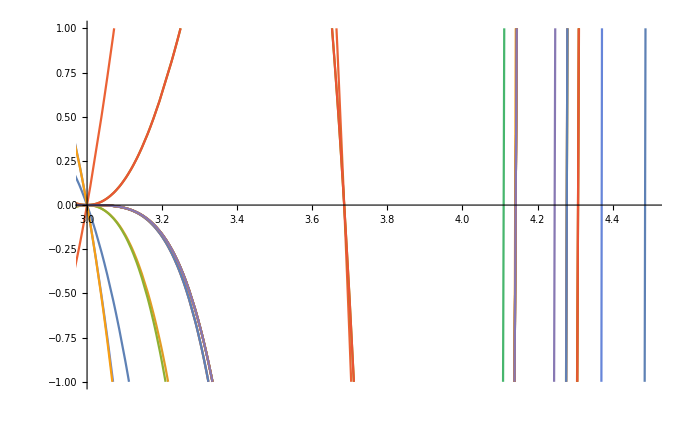

```mathematica
Plot[{1266 x-4577 x^2+6968 x^3-5872 x^4+3011 x^5-966 x^6+190 x^7-21 x^8+x^9,2718 x-8805 x^2+11903 x^3-8904 x^4+4077 x^5-1181 x^6+213 x^7-22 x^8+x^9,2772 x-8940 x^2+12029 x^3-8960 x^4+4089 x^5-1182 x^6+213 x^7-22 x^8+x^9,3246 x-10169 x^2+13247 x^3-9559 x^4+4244 x^5-1202 x^6+214 x^7-22 x^8+x^9,2962 x-9457 x^2+12582 x^3-9265 x^4+4182 x^5-1197 x^6+214 x^7-22 x^8+x^9,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-10608 x+36290 x^2-52903 x^3+43815 x^4-22993 x^5+8005 x^6-1863 x^7+281 x^8-25 x^9+x^10,-9924 x+34358 x^2-50754 x^3+42592 x^4-22614 x^5+7944 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-9932 x+34396 x^2-50811 x^3+42628 x^4-22624 x^5+7945 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10},
{x,2,5},PlotRange->{{3,4.5},{-1,1}}]
```

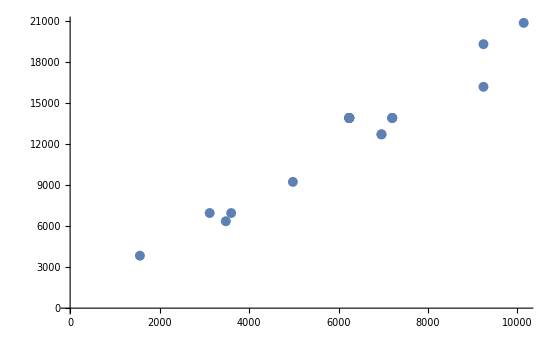

```mathematica
ListPlot[Table[With[{f=First[c],l=Last[c]},
{ChromaticPolynomial[ReadGraph[f[[1]],f[[2]]],5],
ChromaticPolynomial[ReadGraph[l[[1]],l[[2]]],5]}
]
,{c,lists}]]
```

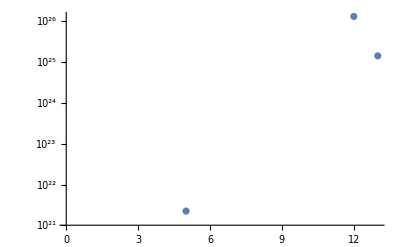

```mathematica
ListLogPlot[Map[Discriminant[#,x]&,{1266 x-4577 x^2+6968 x^3-5872 x^4+3011 x^5-966 x^6+190 x^7-21 x^8+x^9,2718 x-8805 x^2+11903 x^3-8904 x^4+4077 x^5-1181 x^6+213 x^7-22 x^8+x^9,2772 x-8940 x^2+12029 x^3-8960 x^4+4089 x^5-1182 x^6+213 x^7-22 x^8+x^9,3246 x-10169 x^2+13247 x^3-9559 x^4+4244 x^5-1202 x^6+214 x^7-22 x^8+x^9,2962 x-9457 x^2+12582 x^3-9265 x^4+4182 x^5-1197 x^6+214 x^7-22 x^8+x^9,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-10608 x+36290 x^2-52903 x^3+43815 x^4-22993 x^5+8005 x^6-1863 x^7+281 x^8-25 x^9+x^10,-9924 x+34358 x^2-50754 x^3+42592 x^4-22614 x^5+7944 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-9932 x+34396 x^2-50811 x^3+42628 x^4-22624 x^5+7945 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10}]]
```

```mathematica
Map[{Factor[#],Discriminant[#,x]}&,{1266 x-4577 x^2+6968 x^3-5872 x^4+3011 x^5-966 x^6+190 x^7-21 x^8+x^9,2718 x-8805 x^2+11903 x^3-8904 x^4+4077 x^5-1181 x^6+213 x^7-22 x^8+x^9,2772 x-8940 x^2+12029 x^3-8960 x^4+4089 x^5-1182 x^6+213 x^7-22 x^8+x^9,3246 x-10169 x^2+13247 x^3-9559 x^4+4244 x^5-1202 x^6+214 x^7-22 x^8+x^9,2962 x-9457 x^2+12582 x^3-9265 x^4+4182 x^5-1197 x^6+214 x^7-22 x^8+x^9,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-9738 x+33753 x^2-49910 x^3+41924 x^4-22291 x^5+7850 x^6-1844 x^7+280 x^8-25 x^9+x^10,-10608 x+36290 x^2-52903 x^3+43815 x^4-22993 x^5+8005 x^6-1863 x^7+281 x^8-25 x^9+x^10,-9924 x+34358 x^2-50754 x^3+42592 x^4-22614 x^5+7944 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-9932 x+34396 x^2-50811 x^3+42628 x^4-22624 x^5+7945 x^6-1859 x^7+281 x^8-25 x^9+x^10,-8316 x+29592 x^2-45027 x^3+38909 x^4-21227 x^5+7635 x^6-1821 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10,-8154 x+29133 x^2-44514 x^3+38615 x^4-21135 x^5+7620 x^6-1820 x^7+279 x^8-25 x^9+x^10}]
```

{{(-3+x) (-2+x) (-1+x) x (-211+376 x-261 x^2+89 x^3-15 x^4+x^5),-48490363427184},{(-3+x)^2 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^2 (-2+x) (-1+x) x (154-163 x+67 x^2-13 x^3+x^4),0},{(-3+x) (-2+x) (-1+x) x (-541+703 x-378 x^2+107 x^3-16 x^4+x^5),-1782299812811991321600},{(-2+x) (-1+x) x (1481-2507 x+1790 x^2-694 x^3+155 x^4-19 x^5+x^6),2241861553648199247732},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (154-163 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (154-163 x+67 x^2-13 x^3+x^4),0},{(-3+x)^2 (-2+x) (-1+x) x (-541+703 x-378 x^2+107 x^3-16 x^4+x^5),0},{(-3+x)^2 (-2+x) (-1+x) x (-541+703 x-378 x^2+107 x^3-16 x^4+x^5),0},{(-3+x) (-2+x) (-1+x) x (1768-2807 x+1903 x^2-712 x^3+156 x^4-19 x^5+x^6),132491683578369792304742400},{(-3+x) (-2+x) (-1+x) x (1654-2694 x+1866 x^2-708 x^3+156 x^4-19 x^5+x^6),14329830486611739965128704},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-2+x) (-1+x) x (-4966+9749 x-8299 x^2+3991 x^3-1176 x^4+213 x^5-22 x^6+x^7),-4555257996214788295733248},{(-3+x)^3 (-2+x) (-1+x) x (154-163 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0},{(-3+x)^3 (-2+x) (-1+x) x (151-162 x+67 x^2-13 x^3+x^4),0}}

```mathematica
Discriminant[(-3+x) (-2+x) (-1+x) x (-211+376 x-261 x^2+89 x^3-15 x^4+x^5),x]
```

-48490363427184